```mathematica
Clear["Global`*"]
kb=1.38 10^-16;
mp=1.67 10^-24;
μ=0.615;
γ=5/3;
G=6.67 10^-8;
c=3 10^10;
σ=5.67 10^-5; 
Msun=2 10^33;
```

0.908108

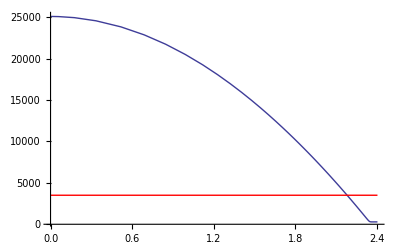

ReplaceAll::reps: {pertsoln} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[GraphicsBox[GraphicsComplexBox[List[List[-0.9999999591836735`, 0.`], List[-0.9607426775969391`, 0.`], List[-0.9181832858290826`, 0.`], List[-0.8784442328596956`, 0.`], List[-0.8394847023622477`, 0.`], List[-0.7972230616836775`, 0.`], List[-0.757781759803577`, 0.`], List[-0.7150383477423542`, 0.`], List[-0.6730744581530703`, 0.`], List[-0.6339309073622561`, 0.`], List[-0.5914852463903196`, 0.`], List[-0.5518599242168528`, 0.`], List[-0.5130141245153249`, 0.`], List[-0.47086621463267486`, 0.`], List[-0.4315386435484944`, 0.`], List[-0.3889089622831917`, 0.`], List[-0.34705880348982804`, 0.`], List[-0.30802898349493396`, 0.`], List[-0.26569705331891763`, 0.`], List[-0.2261854619413709`, 0.`], List[-0.18337176038270195`, 0.`], List[-0.141337581295972`, 0.`], List[-0.10212374100771163`, 0.`], List[-0.05960779053832902`, 0.`], List[-0.01991217886741602`, 0.`], List[0.01900391033155799`, 0.`], List[0.06122210971165424`, 0.`], List[0.10061997029328089`, 0.`], List[0.14331994105602977`, 0.`], List[0.18524038934683965`, 0.`], List[0.22434049883917992`, 0.`], List[0.2667427185126425`, 0.`], List[0.3063245993876354`, 0.`], List[0.3451269577906893`, 0.`], List[0.38723142637486546`, 0.`], List[0.426515556160572`, 0.`], List[0.4691017961274008`, 0.`], List[0.50886769729576`, 0.`], List[0.5478540759921803`, 0.`], List[0.5901425648697227`, 0.`], List[0.6296107149487956`, 0.`], List[0.6723809752089908`, 0.`], List[0.7143717129972469`, 0.`], List[0.7535421119870335`, 0.`], List[0.7960146211579422`, 0.`], List[0.8356667915303814`, 0.`], List[0.8745394394308815`, 0.`], List[0.9167141975125039`, 0.`], List[0.9560686167956567`, 0.`], List[0.9999999591836735`, 0.`], Skeleton[100]], List[]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1.`], List[0, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Automatic]]]], p1, p2].

```mathematica
M=10^7 Msun;
κes=0.4;
(*Calculating effective temperate based on the profile name*)
MyFile="profile-35035-0.1-1000";
MyFileP=StringSplit[MyFile, "-"]//#[[2;;]]&;
MyFileP=ToExpression/@MyFileP;
Σ=MyFileP[[1]];
Ṁ=MyFileP[[2]] 10 4 π G M/(c κes);
R=MyFileP[[3]] 2 G M/c^2;
ν=(Ṁ)/(3π Σ);
Ω=√(G M/R^3);

Teff=((9/8 ν Σ)Ω^2/σ)^0.25;

(*Import profile*)
profile=Import[NotebookDirectory[]<>MyFile,"Table"];
tprofile=profile[[All, {2,4}]];
(*Maximum z for profile*)
zmax=profile[[-1, 2]];


tlow=Position[tprofile[[All,2]], x_/;x<Teff][[1]];
photopos=Extract[tprofile, tlow]//#[[1]]&//#/zmax&
(*Plot temperature and effective temperature for our profile*)
p1=tprofile//ListLinePlot[#, PlotRange->All]&;
p2=Plot[Teff, {z, 0, zmax}, PlotStyle->Directive[Red]];
Show[p1, p2]
tprofile[[All,1]]=tprofile[[All, 1]]/zmax;
tprofile=tprofile//Interpolation;
(*Sound  speed profile*)

cs[z_]:=√((γ kb tprofile[Abs[z]])/(μ mp))
(*cs[z_]:=1*)
cs2[z_]:=cs[z]/cs[0]
(*Defining our perturbation*)
ρ1=1;
σ1=0.1;
(*Perturbation: contains all the info of the   analytic D'alembert solution*)
pert[z_,t_:0]:=1/2(ρ1 ⅇ^((-(z-t)^2)/(2 σ1^2))+ρ1 ⅇ^((-(z+t)^2)/(2 σ1^2)));
(*Endpoint in time to which we would like to evolve the perturbation*)
tmax=1;


(*Solution with non-constant sound speed, based on our temperature profile*)
pertsoln=NDSolve[{(cs2[z])^2 D[ρ[z,t],z,z]-D[ρ[z,t],t,t]==0, ρ[1, t]==0,ρ[-1, t]==0, ρ[z, 0]==pert[z], Derivative[0,1][ρ][z,0]==0},ρ, {z, -1, 1}, {t, 0, tmax}, Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MaxStepSize"->0.002}}];
(*Solution with constant sound speed*)
pertsoln2=NDSolve[{D[ρ[z,t],z,z]-D[ρ[z,t],t,t]==0, ρ[1, t]==0,ρ[-1, t]==0, ρ[z, 0]==pert[z], Derivative[0,1][ρ][z,0]==0},ρ, {z, -1, 1}, {t, 0, tmax}, Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MaxStepSize"->0.002}}];
p1=Table[{photopos,ρ1*i}, {i,0, 1}]//ListLinePlot;
p2=Table[{-photopos,ρ1*i}, {i,0, 1}]//ListLinePlot;
Manipulate[
Show[Plot[{pert[z,t1 ], ρ[z, t1]/.pertsoln, ρ[z, t1]/.pertsoln2}, {z, -1, 1}, PlotRange->{Automatic, {0,1}}, AxesOrigin->{0, 0}], p1, p2],  {t1,0 ,tmax}, ContinuousAction->False, TrackedSymbols:>{t1}
]
```

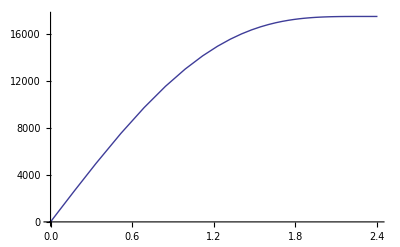

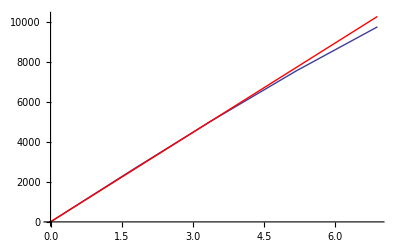

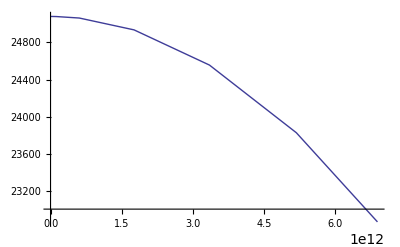

```mathematica
(*Import profile*)
profile=Import[NotebookDirectory[]<>"profile-35035-0.1-1000","Table"];
(*Plot u vs. z*)
profile[[All, {2,1}]]//ListLinePlot[#, PlotRange->All]&
(*Maximum for which u looks linear with z just eyeballing the u vs. z graph*)
zmax=8 10^12;
(*Select all the points in our profile that z less than the above arbitrarily chosen zmax*)
profile2=Select[profile, #[[2]]<zmax&];
(*reset zmax to be the max z in profile2*)
zmax=profile2[[-1, 2]];
(*Find the z closest to zmax/2*)
midpoint=Nearest[profile2[[All, 2]], zmax/2]//Position[profile2[[All, 2]],#[[1]]  ]&//#[[1,1]]&;
(*Calculate the slope using this midpoint*)
m=profile2[[midpoint,1]]/profile2[[midpoint, 2]];
(*m=profile[[1,3]]*)
linapprox[z_]:=m z
p1=profile2[[All, {2,1}]]//ListLinePlot[#, PlotRange->All]&;
p2=Plot[linapprox[z], {z, 0, zmax}, PlotStyle->Directive[Red]];
Show[p1, p2]
profile2[[All,{2,4}]]//ListLinePlot[#, PlotRange->All]&
```

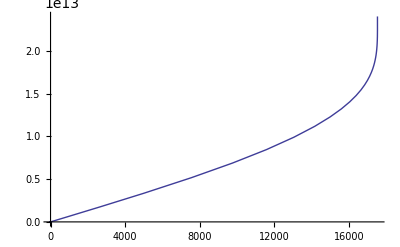

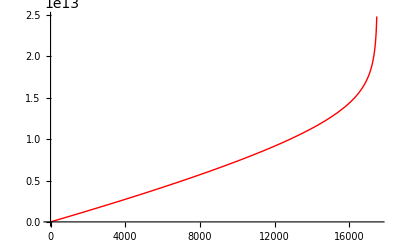

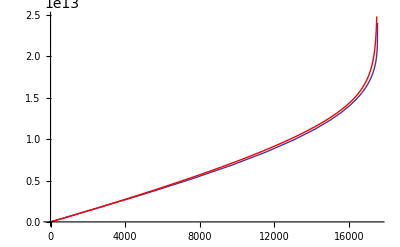

```mathematica
(*Import profile*)
profile=Import[NotebookDirectory[]<>"profile-35035-0.1-1000","Table"];
p1=profile[[All, {1,2}]]//ListLinePlot[#, PlotRange->All]&
ρc=profile[[1,3]];
u0=2 profile[[-1, 1]];
z[u_]:=(u/ρc)/(1-((2u)/u0))^(1/8)

p2=Plot[z[u], {u, 0 , u0/2-1}, PlotStyle->Directive[Red]]
Show[p1, p2]
```